# Neural Networks

Neural networks have emerged in recent years as extremely useful tools in a variety of applications. One area where they have produced particularly impressive results is in image recognition. Recent versions of Mathematica have extensive support for creating neural networks built-in. However, this functionality obscures the details of what a neural network is. In order to understand how neural networks really work, we will explore a very simple network which can be used for recognising handwriting (in particular digits in the range 0-9).

## Handwriting recognition

### Load an image

We start out with a 28x28 matrix of numbers between 0 and 1.

```mathematica
img=;
```

We can use ArrayPlot to visualise this matrix.

```mathematica
ArrayPlot[img,Mesh->True,PlotLegends->Automatic]
```

-Graphics-

In doing so, we recognise that it is actually a greyscale image of a single handwritten number ‘5’.

### A simple neural network

Now let us do some basic manipulations with this matrix. First, we flatten it to a one-dimension vector of size 784 x 1, which we will call ‘x’

```mathematica
x=Flatten[img];
```

```mathematica
Dimensions[x]
```

{784}

We now recall the standard rules of matrix-vector arithmetic. Start with two matrices A of size m_1 x n_1 and B of size m_2 x n_2. We can obtain the product AB of size m_1 x n_2 provided n_1=m_2, and we can compute the product BA of size m_2 x n_1 provided n_2=m_1. We can also compute the sum A+B of size n x m provided n_1=n_2=n and m_1=m_2=m. We can therefore multiply our vector x on the right of a matrix W provided W has size n x 784. Let’s load an example matrix W which happens to have n=10:

```mathematica
W=;
```

```mathematica
Dimensions[W]
```

{10,784}

The product W x is then of size 10 x 1

```mathematica
Dimensions[W.x]
```

{10}

We can add to this a vector that is also of size 10 x 1. Let’s load an example vector b

```mathematica
b=;
```

```mathematica
Dimensions[b]
```

{10}

Now, let us compute W x + b. In doing so, it would be convenient to rescale the components of the resulting vector to be in the range 0-1. One way to achieve this using the logistic sigmoid function

```mathematica
σ=LogisticSigmoid;
```

```mathematica
y=σ[W.x+b];
y//ColumnForm
```

4.26748×10^-6
6.20727×10^-11
1.32467×10^-6
0.614775
5.50255×10^-11
0.838046
5.21637×10^-7
0.0000224692
4.38476×10^-8
5.16372×10^-8

Interestingly, almost all of the numbers are very small, except for the 3rd and 5th elements (counting from zero), with the 5th element being largest. Is it a coincidence that the image represents a handwritten number 5? No, in fact this is one of the simplest examples of a neural network!

All of the magic is in the weight matrix W and the bias vector b. The particular choice of 7850 numbers in W and b efficiently capture how a human writes numbers. Exactly how these were produced is beyond the scope of this exercise, but a simple explanation is that they were obtained by training the neural network with a large corpus of 50,000 example handwritten digits. In fact, this training data is available directly inside Mathematica:

```mathematica
ResourceObject["MNIST"]
```

ResourceObject[…]

In the terminology of neural networks:

x is called the input layer,

the elements of x are called input neurons,

y is called the output layer,

the elements of y are called output neurons,

the elements of the matrix W are called weights,

b is called the bias

σ is called an activation function, and

the whole network, in which output from one layer is used as input to the next is called a feed forward neural network.

### More complicated neural networks: hidden layers

The previous example was an example of a single-layer neural network. It performs reasonably well, but we can do much better by using a more sophisticated neural network. One way we can do this is by introducing a hidden layer, which is just an intermediate step in our matrix-vector multiplication. We now define two weight matrices W_1 (of size 30 x 784) and W_2 (or size 10 x 30) and two bias vectors b_1 (size 30 x 1) and b_2 (10 x 1):

```mathematica
W1=;
b1=;
W2=;
b2=;
```

```mathematica
Dimensions/@{W1,b1,W2,b2}
```

{{30,784},{30},{10,30},{10}}

We can now first multiply W_1 by x, add b_1, and rescale using the logistic sigmoid. This produces an intermediate vector (hidden layer) x_1 of size 30 x 1:

```mathematica
x1=σ[W1.x+b1];
Dimensions[x1]
```

{30}

We can the repeat the process with our other matrix and vector, multiplying W_2 by x_1, adding b_2 and rescaling again

```mathematica
σ[W2.x1+b2]//ColumnForm
```

5.68227×10^-8
0.0000161978
0.0000463367
0.0374157
4.18311×10^-14
0.999807
3.40621×10^-12
2.12025×10^-6
2.63008×10^-10
3.21012×10^-9

Now this appears to perform much better than the single layer network. The matrices W_1 and W_2 and biases b_1 and b_2 were computed using a very similar training process as in the single layer case.

### Deep Networks

We could continue adding layers of sophistication to our network in order to improve accuracy. A complete example can be found in the Neural Networks tutorial. In fact, Mathematica has a more sophisticated deep neural network with several more layers for solving our exact problem. Loading it and trying it out with our input image, it correctly interprets it as the number 5

```mathematica
net=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
net[Image[img]]
```

5

The particular choice of how many layers to include, what sizes the weight matrices should be, etc., are called hyperparameters and are chosen to suit the problem. Many modern neural network tools include the tuning of these hyperparameters as part of the step of training the network.

## Understanding what a neural network sees

So far, we have just treated our neural network as a black box, a function that takes an input (an image of a digit) and produces an output (a number between 0 and 9). We will now try to explore inside the box and understand how the neural network works.

#### Solving for x

Our simple neural network is essentially just finding the y such that y=σ(W.x+b). It is tempting to try turning this around and ask which value of x a given y  corresponds to. This amounts to solving the matrix equation W.x=σ^-1(y)-b for x. Mathematica’s LinearSolve is designed to do exactly that

```mathematica
?LinearSolve
```

Let’s now try this for y corresponding to the digit zero (i.e. the zero-th entry should be close to 1 and the others close to 0)

```mathematica
Y=N[{1-10^-10,10^-10,10^-10,10^-10,10^-10,10^-10,10^-10,10^-10,10^-10,10^-10}];
```

```mathematica
σInv[σ_]:=Log[σ/(1-σ)];
```

```mathematica
Xsol=LinearSolve[W,σInv[Y]-b];
```

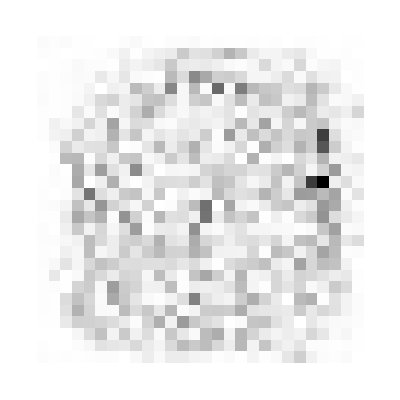

```mathematica
ArrayPlot[Partition[Xsol,28]]
```

This doesn’t look much like the number zero. What has happened? To understand, let’s go back to our original input x with output y and compare it to the corresponding x obtained using LinearSolve with y

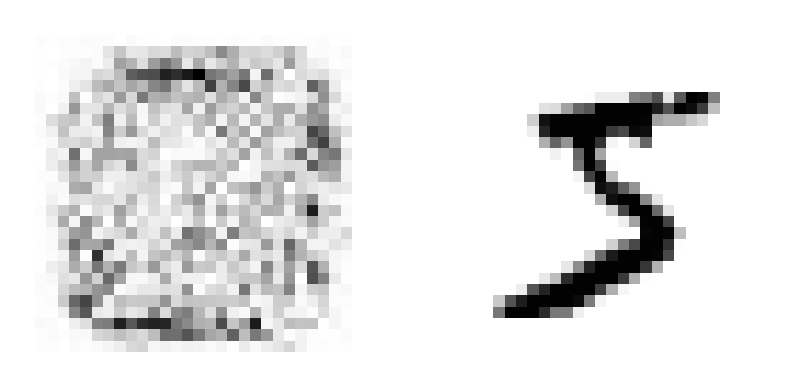

```mathematica
GraphicsRow[{ArrayPlot[Partition[LinearSolve[W,σInv[y]-b],28]],ArrayPlot[img]}]
```

These don’t look at all alike either. The problem is that we have a function that takes 784 (=28*28 pixel image) inputs and returns 10 outputs (one per digit). It is not a 1-1 (injective) function. Equivalently, since W is not a square matrix it does not have an inverse - it is underdetermined. LinearSolve was just giving us one of infinitely-many solutions.

#### Visualising a neural network layer

```mathematica
Dimensions[W]
```

{10,784}

The previous example might suggest that it is hopeless to try to make sense of how our neural network works. There is however, a different way we can try to analyse it. Notice that our matrix W has dimensions 10 x 784. We can equivalently interpret this as 10 vectors of size 1 x 784, or even 10 matrices of size 28 x 28. If we now plot each of those 10 matrices, we notice something interesting: if we look carefully we notice that they appear to be slightly fuzzy versions of the digits 0 to 9!

```mathematica
Map[Image[Partition[#,28],ImageSize->100]&,σ[W]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
b
```

{-6.01659,-0.810177,-3.17849,-5.37082,-2.11677,0.850661,-5.90874,-0.795553,-11.0805,-6.09041}

#### Visualising the two-layer network

We can similarly try to visualise our two-layer network. Recall that this consisted of two matrices: W_1 of size 30 x 784 and W_2 of size 10 x 30. Taking W_1 first, we can split this into 30 images. In doing so, we see that each image is capturing a feature such as a vertical or horizontal line.

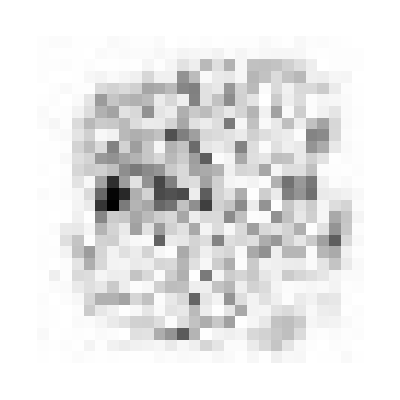
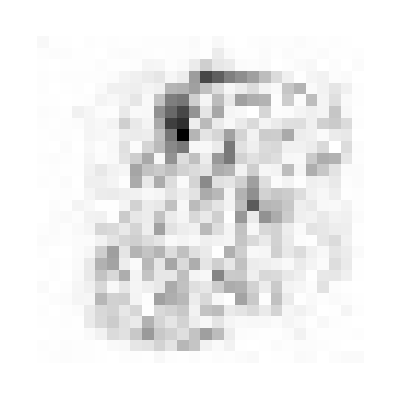
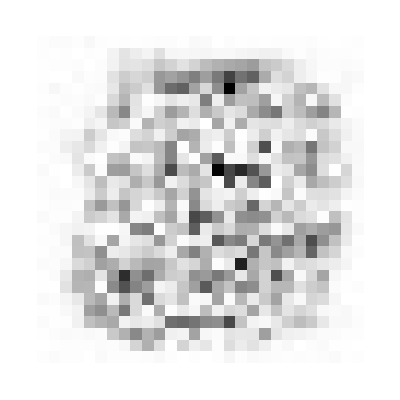
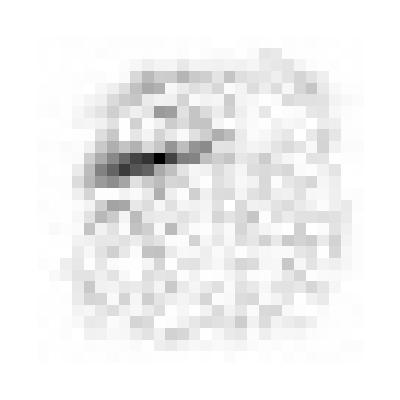
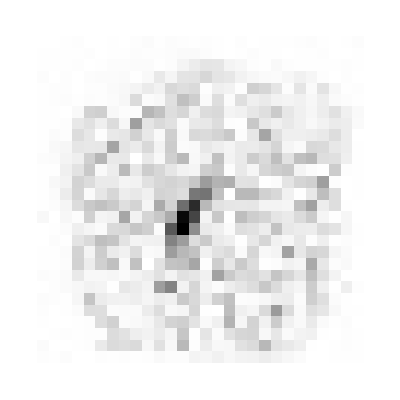
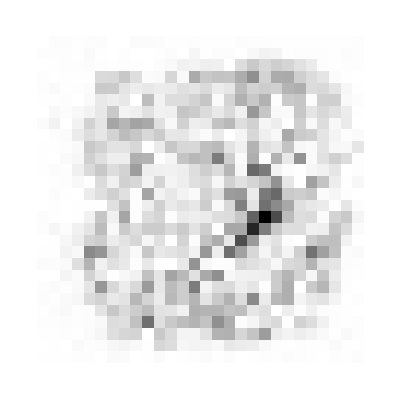
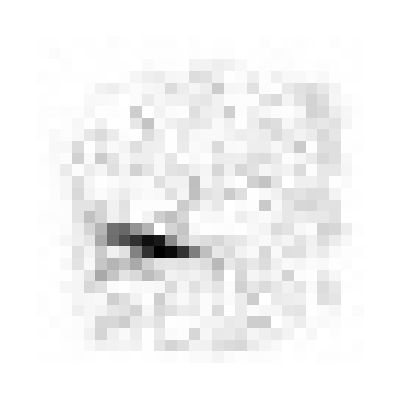
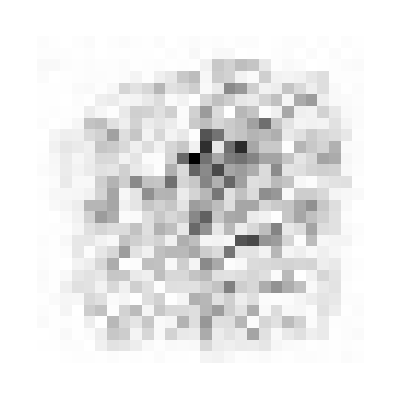

```mathematica
Map[ArrayPlot[Partition[#,28]]&,W1]
```

We might then interpret W_2 as capturing how these features are combined to produce a digit.